```mathematica
grainyImg=-Graphics-
```

-Graphics-

```mathematica
(* 
1. Convert the image to grayscale;
2. Create a binary image with ones and zeros
*)
```

```mathematica
binImg=Binarize[ColorConvert[grainyImg,"Grayscale"]]
```

-Graphics-

```mathematica
(* ho many pixels are black? *)
```

```mathematica
Count[Flatten[ImageData[binImg]],1]
```

59138

```mathematica
(* Repeat the procedure by bluring the image *)
```

```mathematica
blurredImg=ColorConvert[Blur[grainyImg,3],"Grayscale"]
```

-Graphics-

```mathematica
Binarize[blurredImg]
```

-Graphics-

```mathematica
Count[Flatten[ImageData[Binarize[blurredImg]]],1]
```

112342

```mathematica
Blur[grainyImg,4]
```

-Graphics-

```mathematica
Binarize[
ColorConvert[Blur[grainyImg,4],"Grayscale"],0.3
]
```

-Graphics-

```mathematica
lst=Table[
Count[
Flatten[
ImageData[
Binarize[
ColorConvert[Blur[grainyImg,n],"Grayscale"],0.3
]
]
],1],{n,0,10,1}
]
```

{27177,21725,12009,5905,2988,1599,1090,971,937,901,854}

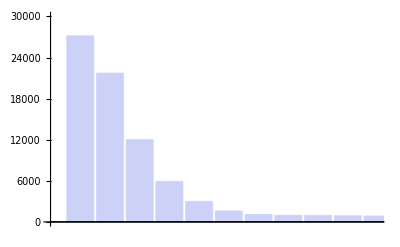

```mathematica
BarChart[lst,PlotRange->{{0,11},{0,30000}}]
```

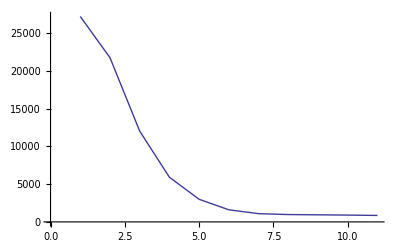

```mathematica
ListLinePlot[lst,PlotRange->Automatic]
```